# LO coefficient (Mellin transform of the LO pt-distribution)

```mathematica
C0gg[αs_,n_]:=(2 αs CA)/π 1/ξp(Gamma[1/2]Gamma[n])/Gamma[n+1/2](Hypergeometric2F1[1/2,n,n+1/2,(√(1+ξp)-√ξp)^4]-2(1+ξp)/(√(1+ξp)+√ξp)^2 n/(n+1/2) Hypergeometric2F1[1/2,n+1,n+3/2,(√(1+ξp)-√ξp)^4] + ((1+ξp)(3+ξp))/(√(1+ξp)+√ξp)^4(n(n+1))/((n+1/2)(n+3/2))Hypergeometric2F1[1/2,n+2,n+5/2,(√(1+ξp)-√ξp)^4]-2(1+ξp)/(√(1+ξp)+√ξp)^6 (n(n+1)(n+2))/((n+1/2)(n+3/2)(n+5/2)) Hypergeometric2F1[1/2,n+3,n+7/2,(√(1+ξp)-√ξp)^4] + 1/(√(1+ξp)+√ξp)^8(n(n+1)(n+2)(n+3))/((n+1/2)(n+3/2)(n+5/2)(n+7/2))Hypergeometric2F1[1/2,n+4,n+9/2,(√(1+ξp)-√ξp)^4]);
```

## Expansion in small-N

```mathematica
Series[C0gg[αs,n],{n,0,-1}]
```

(31250 αs)/(3 π n)+O[n]^0

# Physical constants

```mathematica
nc=3;nf=5;
CA=nc;CF=(nc^2-1)/(2nc);
β0=1/(12 π)(11 CA-2nf);(*A.1.3a*)
β1=(17 CA^2-(5CA+3CF)nf)/(24 π^2);(*A.1.3b*)
GF=1.166378 10^-5;
GevtoPb=3.8937966 10^8;
σ0[αs_]:=(αs^2 √2 GF)/(576π); (*C.1.3*)
A1g=CA/π;B1g=-β0;
A2g=CA/(2 π^2)(CA(67/18-Zeta[2])-5/9 nf);
A3g=CA/π^3((245/96-67/36 Zeta[2]+11/8 Zeta[4]+11/24 Zeta[3])CA^2+(5/18 Zeta[2]-209/432-7/12 Zeta[3])nf CA+(1/2 Zeta[3]-55/96)nf CF-1/108 nf^2);
β2=1/(4π)^3(2857/54 CA^3+(CF^2-205/18 CA CF-1415/54 CA^2)nf+(11/9 CF+77/54 CA)nf^2);
B2g=1/(16 π^2)(CA^2(-611/9+88/3 Zeta[2]+16 Zeta[3])+nf CA (428/27-16/3 Zeta[2])+2nf CF-20/27 nf^2);
```

# dσ/dpt

The HE approx of dσ/dptdy is given in Eqs. 3.4.17-3.4.18 of Muselli's thesis, setting b=0 will give dσ/dpt. The same result is found in x-space in Eqs. 4.12-4.13 of the Forte,Muselli paper as a series in Log[x]^k, of which the Mellin transform is also included below.

## Mellin transform

```mathematica
f[n_,k_]:=Assuming[{Element[k,Integers],k≥ 1,n>0 },Integrate[x^(n-1)Log[x]^(k-1)/((k-1)!),{x,0,1}]]
```

```mathematica
f[n,k]
```

(-1)^(1+k) n^-k

```mathematica
Table[f[n,k],{k,1,2}]
```

{1/n,-1/n^2}

## Results

```mathematica
ExpdσggLOFO[αs_,n_,pt_]:=(2 pt)/mH^2 (GevtoPb)σ0[αs]C0gg[αs,n]
```

```mathematica
ExpdσggLOHE[αs_,n_,pt_]:=(2 pt)/mH^2 (GevtoPb)σ0[αs](2 CA αs)/(π ξp n)
```

```mathematica
(*input variables*)
mH=125;
αss=0.11263992085801;
nn=0.2;
pt=100;
ξp=(pt/mH)^2;
```

```mathematica
(*FO@LO benchmarked against HpT-MON*)
```

```mathematica
ExpdσggLOFO[αss,nn,pt]
```

0.00102811

```mathematica
(*HE approx at LO benchmarked against HpT-N3LO*)
```

```mathematica
ExpdσggLOHE[αss,nn,pt]
```

0.000968799

```mathematica
(* Ratio FO/HE *)
```

```mathematica
ExpdσggLOFO[αss,nn,pt]/ExpdσggLOHE[αss,nn,pt]
```

1.06123

```mathematica
atilde[ξ_]:=(√(ξ+1)+√ξ)^2
a[ξ_]:=(√(ξ+1)-√ξ)^2
FO[ξ_]:=Log[(1-a[ξ])/2]+2Log[(atilde[ξ]-1)/2]
resum[ξ_]:=Log[atilde[ξ]/ξ]
```

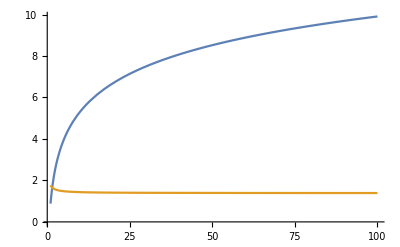

```mathematica
Plot[{FO[ξ],resum[ξ]},{ξ,1,100}]
```